```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Initial Params*)
params = Import["/home/sarah/transients-simulations/python36/config.ini","Ini"]
```

<|INITIAL PARAMETERS→<|n_sources → 2e6  ,fl_min → 1e-1   ,fl_max → 1e7   ,flux_err → 1e-1  ,dmin → 1e-1 ,dmax → 1e5    ,det_threshold → 5 ,extra_threshold → 3  ,file → output   ,lightcurvetype → gaussian |>,SIM→<|nobs → 46 ,obssens → 31.7e-6 ,obssig → 4.6e-6 ,obsinterval → 7,obsdurations → 0.009 |>|>

```mathematica
startexec = DateObject[];
nsources = ToExpression[StringReplace[params[[1]][[1]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
fluxmin =ToExpression[StringReplace[params[[1]][[2]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
fluxmax =ToExpression[StringReplace[params[[1]][[3]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
fluxerr =ToExpression[StringReplace[params[[1]][[4]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
dmin =ToExpression[StringReplace[params[[1]][[5]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
dmax = ToExpression[StringReplace[params[[1]][[6]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
detThreshold = ToExpression[StringReplace[params[[1]][[7]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
extraThreshold =ToExpression[StringReplace[params[[1]][[8]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
file = StringDelete[params[[1]][[9]]," "];
transientType =StringDelete[params[[1]][[10]]," "];
nobs =ToExpression[StringReplace[params[[2]][[1]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
obssens=ToExpression[StringReplace[params[[2]][[2]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
obssig=ToExpression[StringReplace[params[[2]][[3]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
obsinterval=ToExpression[StringReplace[params[[2]][[4]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
obsdur = ToExpression[StringReplace[params[[2]][[5]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
```

```mathematica
(*Simulate Observations*)
(*start, dur, sensitivity. in Days and Jy.Choice of Gaussian and its characteristics were arbitrary.*)
obs =Table[{UnixTime[]/(60*60*24)+i*obsinterval //N,obsdur,RandomVariate[NormalDistribution[obssens,obssig]]*detThreshold},{i,1,nobs}];
```

```mathematica
obs[[1;;3]]
```

{{18212.9,0.009,0.000197787},{18219.9,0.009,0.000197554},{18226.9,0.009,0.00017237}}

```mathematica
stats = Import["/home/sarah/transients-simulations/python36/"<>file<>"_"<>transientType<>"_Stat"][[2;; , 1;;3]];
gaps = Table[obs[[i+1,1]]-obs[[i,1]]+obs[[i,2]],{i,1,Length[obs]-1}];
durmax = obs[[Length[obs],1]]+obs[[Length[obs],2]]-obs[[1,1]];
sensmaxgaps=obs[[Flatten[Position[gaps,n_/;n==Max[gaps]]]+1,3]][[1]];
durmaxfred[x_]:=(((1.+fluxerr)*obs[[Length[obs],3]]*obs[[1,2]])/x)/(ⅇ^(-(durmax-obs[[1,2]]+x)/x)-ⅇ^(-((durmax+x)/x)));
maxdistfred[x_]:=(((1.+fluxerr)*sensmaxgaps*obs[[1,2]])/x)/(ⅇ^(-Max[gaps]/x)-ⅇ^(-((Max[gaps]+obs[[1,2]])/x)));
If[transientType == "tophat", gridlines = {{obs[[1,2]],durmax,Max[gaps] },{Min[obs[[1;; , 3]]],Max[obs[[1;; , 3]]],Max[obs[[1;; , 3]]]/detThreshold*(extraThreshold+detThreshold)}}]
If[transientType == "fred", gridlines = {{obs[[1,2]]},{Min[obs[[1;; , 3]]],Max[obs[[1;; , 3]]],Max[obs[[1;; , 3]]]/detThreshold*(extraThreshold+detThreshold)}}]
If[(transientType ≠"fred") && (transientType≠"tophat"),gridlines = {{obs[[1,2]]},{Min[obs[[1;; , 3]]],Max[obs[[1;; , 3]]],Max[obs[[1;; , 3]]]/detThreshold*(extraThreshold+detThreshold)}}]
```

{{0.009},{0.000109873,0.000201189,0.000321903}}

```mathematica
ListPointPlot3D[stats[[1;;,1;;3]],PlotLegends->Automatic,ScalingFunctions->{"Log10","Log10",Automatic}]
```

-Graphics3D-

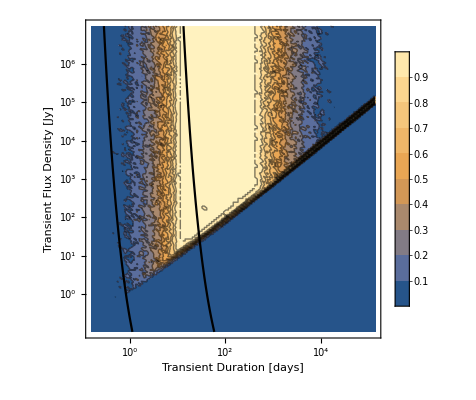

```mathematica
lines = Quiet[Plot[{durmaxfred[x],maxdistfred[x]},{x,Min[stats[[1;; , 1]]],Max[stats[[1;; ,1]]]},PlotRange->{{Min[stats[[1;; , 1]]],Max[stats[[1;; ,1]]]},{Min[stats[[1;; , 2]]],Max[stats[[1;; ,2]]]}},PlotStyle->Directive[Thick,Black],ScalingFunctions->{"Log10","Log10"}]];
If[transientType =="tophat",ListContourPlot[stats[[1;;,1;;3]],PlotLegends->Automatic,ScalingFunctions->{"Log10","Log10",Automatic},GridLines->gridlines,GridLinesStyle->Directive[Thick,Black],FrameLabel->{"Transient Duration [days]","Transient Flux Density [Jy]"}],ListContourPlot[stats[[1;;,1;;3]],PlotLegends->Automatic,ScalingFunctions->{"Log10","Log10",Automatic},GridLines->gridlines,GridLinesStyle->Directive[Thick,Black],FrameLabel->{"Transient Duration [days]","Transient Flux Density [Jy]"},Epilog->lines[[1]]]]
```